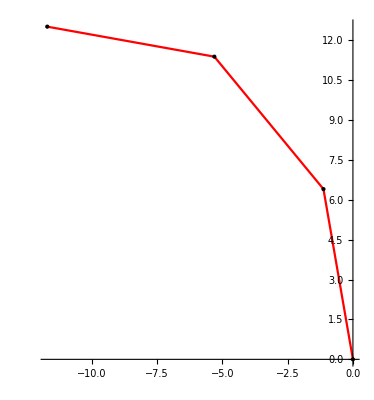

Nilai Theta1 : 100

Nilai Theta2 : 120

Nilai Theta3 : 130

Base   ke Servo1 : ( 0 , 0 )

Servo1 ke Servo2 : ( -1.12871 , 6.40125 )

Servo2 ke Servo3 : ( -5.30683 , 11.3805 )

Servo3 ke Edge   : ( -11.7081 , 12.5093 )

```mathematica
angle1=100; angle2=120;angle3=130;base = 0;humerus = 6.5;ulna= 6.5;carpus = 6.5;theta1 = angle1;theta2 = angle2-90;theta3 = angle3-90;
s1= Sin[theta1 Degree];s2 = Sin[theta1 Degree + theta2 Degree];s3 = Sin[theta1 Degree + theta2 Degree + theta3 Degree];
c1= Cos[theta1 Degree];c2 = Cos[theta1 Degree + theta2 Degree];c3 = Cos[theta1 Degree + theta2 Degree + theta3 Degree];
h1= s1*humerus; h2= s2*ulna;h3= s3*carpus;d1= c1*humerus; d2= c2*ulna;d3= c3*carpus;height = h1+h2+h3;depth = d1+d2+d3;
Print[ListLinePlot[{{0,base},{d1,h1},{d1+d2,h1+h2},{depth,height}},PlotStyle->Red,  AspectRatio->Automatic,Mesh->All, MeshStyle->{Black,PointSize[Large]}]] 
Print ["Nilai Theta1 : ",angle1];Print ["Nilai Theta2 : ",angle2];Print ["Nilai Theta3 : ",angle3];
Print["Base   ke Servo1 : ( ", 0," , ",base," )"];Print["Servo1 ke Servo2 : ( ", d1," , ",h1," )"]
Print["Servo2 ke Servo3 : ( ", d1+d2," , ",h1+h2," )"];Print["Servo3 ke Edge   : ( ", depth," , ",height," )"]
```